## Construct and Parameterize One Enzyme Module

```mathematica
Quit[]
```

## Initializing the Notebook

```mathematica
<<Toolbox`;
<<MASSef`;

SetDirectory[NotebookDirectory[]];

removeInputFiles = True;
removeOutputFiles = True;

rxnName="PFK2";
fitLabel=rxnName;
dataFileName=rxnName;

assumedUncertaintyFraction = 0.05;
(*Q10 Correction Options*)
Q10KcatCorrectionFlag = True; (*True if kcats should be corrected to physiological T*)
TPhysiological = 37; (*C*)
Q10=2.5;


(* user will need to change this path *)
(*pathMASSef = "/Users/guest/Desktop/internship stuff/MASSef_1/";*)
pathMASSef = "C:/MASSef/";
kineticDataFileName =  "kinetic_data_MASSpy.csv";

mainFolder = "fit_PFK2_MASSpy_typeII";
{pathData, inputPath, outputPath}=initializeNotebook[pathMASSef, mainFolder, removeInputFiles, removeOutputFiles];
```

Molecule::shdw: Symbol Molecule appears in multiple contexts {AutomaticUnits`,System`}; definitions in context AutomaticUnits` may shadow or be shadowed by other definitions.

Working dir:C:\MASSef\examples\

## Import Data

```mathematica
{rxn, mechanism, structure, nActiveSites, nAllostericSites, KeqList0,kmList0, s05List0, kcatList0, inhibitionList0, activationList0, otherParmsList0, bufferInfo, ionCharge}= importAllData [rxnName, pathData, kineticDataFileName, assumedUncertaintyFraction, Q10KcatCorrectionFlag, TPhysiological, Q10];
```

(atp^c+f6p^c→adp^c+fdp^c+h^c)^PFK2

Null;

Structure:

Active sites:

Keq Values:

Priority | Substrate | Keq_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | atp | Null
f6p | Null | 2000 | 1900.
2100. | Null | Null | 7.5 | Null | Null | Null

Km Values:

Priority | Substrate | Km_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | atp | 8.×10^-6 | 7.6×10^-6
8.4×10^-6 |  |  | 7.5 | 25 |  | 
1 | f6p | 6.×10^-6 | 5.7×10^-6
6.3×10^-6 |  |  | 7.5 | 25 |  | 
1 | atp | 0.00002 | 0.000019
0.000021 |  |  | 8.2 | 26 |  | 
1 | f6p | 0.0001 | 0.000095
0.000105 |  |  | 8.2 | 26 |  |

S0.5 Values:

Priority | Substrate | S0.5_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

kcat Values:

Priority | Metabolite(s) | Value | Uncertainty | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | atp | Null
f6p | Null | 145.214 | 139.735
145.214 |  | 8.2 | 37 |  |

Inhibition Values:

Priority | Parameter_Type | Inhibitor | Value | Uncertainty | Cosubstrates | Inhibition Type | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

Activation Values:

Priority | Parameter_Type | Activator | Value | Uncertainty | Cosubstrates | Activation Type | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

Other Parameters:

Priority | Parameter_Type | Metabolite | Value | Uncertainty | Cosubstrates | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

### Define data points priority

```mathematica
(* data point priorities should be between 0 and 1 
  if a given data point has priority 0, it will be discarded
  by default all data points priority is set to 1 *)

KeqPriorities = {1};
kmPriorities = {1,1,1,1};
s05Priorities = Null;
kcatPriorities = {1};
inhibitionPriorities=Null;
activationPriorities = Null;
otherParamsPriorities = Null;

{KeqList, kmList, s05List, kcatList, inhibitionList, activationList, otherParmsList}= updateDataPriorities[KeqPriorities, kmPriorities, s05Priorities, kcatPriorities, inhibitionPriorities, activationPriorities, otherParamsPriorities,
					 KeqList0,kmList0, s05List0, kcatList0, inhibitionList0, activationList0, otherParmsList0];

printEnzymeData[rxn, mechanism, structure, nActiveSites,  KeqList, kmList, s05List, kcatList, inhibitionList, activationList, otherParmsList];
```

(atp^c+f6p^c→adp^c+fdp^c+h^c)^PFK2

Null;

Structure:

Active sites:

Keq Values:

Priority | Substrate | Keq_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | atp | Null
f6p | Null | 2000 | 1900.
2100. | Null | Null | 7.5 | Null | Null | Null

Km Values:

Priority | Substrate | Km_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | atp | 8.×10^-6 | 7.6×10^-6
8.4×10^-6 |  |  | 7.5 | 25 |  | 
1 | f6p | 6.×10^-6 | 5.7×10^-6
6.3×10^-6 |  |  | 7.5 | 25 |  | 
1 | atp | 0.00002 | 0.000019
0.000021 |  |  | 8.2 | 26 |  | 
1 | f6p | 0.0001 | 0.000095
0.000105 |  |  | 8.2 | 26 |  |

S0.5 Values:

Priority | Substrate | S0.5_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

kcat Values:

Priority | Metabolite(s) | Value | Uncertainty | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | atp | Null
f6p | Null | 145.214 | 139.735
145.214 |  | 8.2 | 37 |  |

Inhibition Values:

Priority | Parameter_Type | Inhibitor | Value | Uncertainty | Cosubstrates | Inhibition Type | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

Activation Values:

Priority | Parameter_Type | Activator | Value | Uncertainty | Cosubstrates | Activation Type | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

Other Parameters:

Priority | Parameter_Type | Metabolite | Value | Uncertainty | Cosubstrates | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

## Define enzyme mechanism and catalytic tracks

### Define enzyme mechanism

```mathematica
Overscript[atp^c+f6p^c->adp^c+fbp^c+h^c, PFK2]
```

```mathematica
catalyticBranch={"E_PFK2[c] + f6p[c] <=> E_PFK2[c]&f6p",
				"E_PFK2[c]&f6p + atp[c] <=> E_PFK2[c]&f6p&atp",

				"E_PFK2[c]&f6p&atp <=> E_PFK2[c]&fdp&adp",
				
				"E_PFK2[c]&fdp&adp <=> E_PFK2[c]&fdp + adp[c]",
				"E_PFK2[c]&fdp <=> E_PFK2[c] + fdp[c]"};


enzymeModel=constructEnzymeModule[Mechanism->catalyticBranch,Activators->{},ActivationSites->0,Inhibitors->{},InhibitionSites->0];
enzymeModel["Reactions"]
```

{((PFK2^c)_^+f6p^c⇌(PFK2^c&f6p^c)_^)^PFK21,((PFK2^c&fdp^c)_^⇌(PFK2^c)_^+fdp^c)^PFK22,((PFK2^c&f6p^c)_^+atp^c⇌(PFK2^c&f6p^c&atp^c)_^)^PFK23,((PFK2^c&fdp^c&adp^c)_^⇌(PFK2^c&fdp^c)_^+adp^c)^PFK24,((PFK2^c&f6p^c&atp^c)_^⇌(PFK2^c&fdp^c&adp^c)_^)^PFK25}

### Define all catalytic tracks

```mathematica
catalyticReactionsSet1={((PFK2^c)_^+f6p^c⇌(PFK2^c&f6p^c)_^)^PFK21,Overscript[(PFK2^c&fdp^c)_^⇌(PFK2^c)_^+fdp^c, PFK22],((PFK2^c&f6p^c)_^+atp^c⇌(PFK2^c&f6p^c&atp^c)_^)^PFK23,Overscript[(PFK2^c&fdp^c&adp^c)_^⇌(PFK2^c&fdp^c)_^+adp^c, PFK24],((PFK2^c&f6p^c&atp^c)_^⇌(PFK2^c&fdp^c&adp^c)_^)^PFK25};
catalyticReactionsSetsList = {catalyticReactionsSet1};
```

## Set up rate equations

```mathematica
MWCFlag=False;
nActiveSites=1;
assumedSaturatingConc = 1;
simplifyFlag=True;
simplifyMaxTime=30;
otherMetsReverseZeroSub={};
otherMetsForwardZeroSub ={};

{enzymeModel, haldaneRatiosList,  metSatForSub, metSatRevSub,  finalRateConsts, metsFull, metsSub, rateConstsSub, 
			fileList, fileListSub, eqnNameList,eqnValList, eqnValListPy, 
			allCatalyticReactions,nonCatalyticReactions, unifiedRateConstList, 
			absoluteFlux, absoluteRateForward, absoluteRateReverse, relativeRateForward, relativeRateReverse, 
			otherAbsoluteRatesForward, otherAbsoluteRatesReverse}=

	setUpRateEquations[enzymeModel, rxn, rxnName, inputPath, inhibitionList, inhibitionList, catalyticReactionsSetsList, otherMetsReverseZeroSub,  
						 otherMetsForwardZeroSub,  MWCFlag, simplifyFlag, simplifyMaxTime, nActiveSites, assumedSaturatingConc];
```

Added inhibition reactions:

{}

Generating flux equation...

{((PFK2^c&f6p^c&atp^c)_^-((PFK2^c&fdp^c&adp^c)_^)/K_PFK25) Volume_c k_PFK25^⟶}

Volume_c (-(PFK2^c&fdp^c&adp^c)_^ k_PFK25^⟵+(PFK2^c&f6p^c&atp^c)_^ k_PFK25^⟶)

Simplifying...

Generating absolute rate forward equation...

Simplifying...

Generating absolute rate reverse equation...

Simplifying...

Generating relative rate forward equation...

Simplifying...

Generating relative rate forward equation...

Simplifying...

Generating relative rate reverse equation...

Simplifying...

Generating relative rate reverse equation...

Simplifying...

Generating Haldane Relations...

Defining rate constant and metabolite substitutions for export...

Exporting equations...

## Simulate Data

```mathematica
(* format: {priority, ratio or other custom equation, value, value range (uncertainty) *)
customRatiosDataList={};
```

### Simulate data without uncertainty

```mathematica
{allFittingData, dataPathList, fileList, fileListSub}= simulateData[enzymeModel,dataFileName,fitLabel, haldaneRatiosList, KeqList, kmList, s05List, kcatList, inhibitionList, activationList, otherParmsList, rxn, metsFull,  
			metSatForSub, metSatRevSub,  bufferInfo, ionCharge, inputPath,  fileList, fileListSub, 
			eqnNameList,eqnValList, eqnValListPy, eqnNameList, rateConstsSub, 
			metsSub, allCatalyticReactions,nonCatalyticReactions, unifiedRateConstList, customRatiosDataList, assumedSaturatingConc];
```

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

```mathematica
FilePrint@dataPathList
```

Priority	adp[c]	atp[c]	f6p[c]	fdp[c]	param_PFK2_total	param_pH	param_Temp	FileFlag	Target_Data
1	0	0	0	0	1	7.5	25	"C:\MASSef\examples\fit_PFK2_MASSpy_typeII\input\haldaneRatio_1.txt"	2000
1	0	0	0	0	1	7.5	25	"C:\MASSef\examples\fit_PFK2_MASSpy_typeII\input\haldaneRatio_1.txt"	2000
1	0	0	0	0	1	7.5	25	"C:\MASSef\examples\fit_PFK2_MASSpy_typeII\input\haldaneRatio_1.txt"	2000
1	0	0	0	0	1	7.5	25	"C:\MASSef\examples\fit_PFK2_MASSpy_typeII\input\haldaneRatio_1.txt"	2000
1	0	0	0	0	1	7.5	25	"C:\MASSef\examples\fit_PFK2_MASSpy_typeII\input\haldaneRatio_1.txt"	2000
1	0	0	0	0	1	7.5	25	"C:\MASSef\examples\fit_PFK2_MASSpy_typeII\input\haldaneRatio_1.txt"	2000
1	0	0	0	0	1	7.5	25	"C:\MASSef\examples\fit_PFK2_MASSpy_typeII\input\haldaneRatio_1.txt"	2000
1	0	0	0	0	1	7.5	25	"C:\MASSef\examples\fit_PFK2_MASSpy_typeII\input\haldaneRatio_1.txt"	2000
1	0	0	0	0	1	7.5	25	"C:\MASSef\examples\fit_PFK2_MASSpy_typeII\input\haldaneRatio_1.txt"	2000
1	0	0	0	0	1	7.5	25	"C:\MASSef\examples\fit_PFK2_MASSpy_typeII\input\haldaneRatio_1.txt"	2000
1	0	0	0	0	1	7.5	25	"C:\MASSef\examples\fit_PFK2_MASSpy_typeII\input\haldaneRatio_1.txt"	2000
1	0	8.000000000000003e-7	1	0	1	7.5	25	"C:\MASSef\examples\fit_PFK2_MASSpy_typeII\input\relRateFor_atp.txt"	0.09090909090909094
1	0	1.267914553968892e-6	1	0	1	7.5	25	"C:\MASSef\examples\fit_PFK2_MASSpy_typeII\input\relRateFor_atp.txt"	0.1368068886032101
1	0	2.0095091452076667e-6	1	0	1	7.5	25	"C:\MASSef\examples\fit_PFK2_MASSpy_typeII\input\relRateFor_atp.txt"	0.20076000891310197
1	0	3.1848573644279767e-6	1	0	1	7.5	25	"C:\MASSef\examples\fit_PFK2_MASSpy_typeII\input\relRateFor_atp.txt"	0.28474724895080133
1	0	5.047658755841546e-6	1	0	1	7.5	25	"C:\MASSef\examples\fit_PFK2_MASSpy_typeII\input\relRateFor_atp.txt"	0.386863179846857
1	0	8.000000000000003e-6	1	0	1	7.5	25	"C:\MASSef\examples\fit_PFK2_MASSpy_typeII\input\relRateFor_atp.txt"	0.5000000000000001
1	0	0.000012679145539688918	1	0	1	7.5	25	"C:\MASSef\examples\fit_PFK2_MASSpy_typeII\input\relRateFor_atp.txt"	0.6131368201531432
1	0	0.000020095091452076665	1	0	1	7.5	25	"C:\MASSef\examples\fit_PFK2_MASSpy_typeII\input\relRateFor_atp.txt"	0.7152527510491988
1	0	0.000031848573644279767	1	0	1	7.5	25	"C:\MASSef\examples\fit_PFK2_MASSpy_typeII\input\relRateFor_atp.txt"	0.7992399910868982
1	0	0.00005047658755841546	1	0	1	7.5	25	"C:\MASSef\examples\fit_PFK2_MASSpy_typeII\input\relRateFor_atp.txt"	0.86319311139679
1	0	0.00008000000000000003	1	0	1	7.5	25	"C:\MASSef\examples\fit_PFK2_MASSpy_typeII\input\relRateFor_atp.txt"	0.9090909090909091
1	0	1	6.000000000000003e-7	0	1	7.5	25	"C:\MASSef\examples\fit_PFK2_MASSpy_typeII\input\relRateFor_f6p.txt"	0.09090909090909095
1	0	1	9.50935915476669e-7	0	1	7.5	25	"C:\MASSef\examples\fit_PFK2_MASSpy_typeII\input\relRateFor_f6p.txt"	0.1368068886032101
1	0	1	1.50713185890575e-6	0	1	7.5	25	"C:\MASSef\examples\fit_PFK2_MASSpy_typeII\input\relRateFor_f6p.txt"	0.20076000891310194
1	0	1	2.388643023320983e-6	0	1	7.5	25	"C:\MASSef\examples\fit_PFK2_MASSpy_typeII\input\relRateFor_f6p.txt"	0.2847472489508014
1	0	1	3.78574406688116e-6	0	1	7.5	25	"C:\MASSef\examples\fit_PFK2_MASSpy_typeII\input\relRateFor_f6p.txt"	0.38686317984685703
1	0	1	6.000000000000003e-6	0	1	7.5	25	"C:\MASSef\examples\fit_PFK2_MASSpy_typeII\input\relRateFor_f6p.txt"	0.5000000000000001
1	0	1	9.509359154766689e-6	0	1	7.5	25	"C:\MASSef\examples\fit_PFK2_MASSpy_typeII\input\relRateFor_f6p.txt"	0.6131368201531433
1	0	1	0.000015071318589057501	0	1	7.5	25	"C:\MASSef\examples\fit_PFK2_MASSpy_typeII\input\relRateFor_f6p.txt"	0.7152527510491988
1	0	1	0.000023886430233209828	0	1	7.5	25	"C:\MASSef\examples\fit_PFK2_MASSpy_typeII\input\relRateFor_f6p.txt"	0.7992399910868981
1	0	1	0.0000378574406688116	0	1	7.5	25	"C:\MASSef\examples\fit_PFK2_MASSpy_typeII\input\relRateFor_f6p.txt"	0.86319311139679
1	0	1	0.00006000000000000003	0	1	7.5	25	"C:\MASSef\examples\fit_PFK2_MASSpy_typeII\input\relRateFor_f6p.txt"	0.9090909090909091
1	0	2.0000000000000003e-6	1	0	1	8.2	26	"C:\MASSef\examples\fit_PFK2_MASSpy_typeII\input\relRateFor_atp.txt"	0.09090909090909091
1	0	3.1697863849222286e-6	1	0	1	8.2	26	"C:\MASSef\examples\fit_PFK2_MASSpy_typeII\input\relRateFor_atp.txt"	0.13680688860321005
1	0	5.023772863019165e-6	1	0	1	8.2	26	"C:\MASSef\examples\fit_PFK2_MASSpy_typeII\input\relRateFor_atp.txt"	0.20076000891310186
1	0	7.96214341106994e-6	1	0	1	8.2	26	"C:\MASSef\examples\fit_PFK2_MASSpy_typeII\input\relRateFor_atp.txt"	0.2847472489508013
1	0	0.000012619146889603861	1	0	1	8.2	26	"C:\MASSef\examples\fit_PFK2_MASSpy_typeII\input\relRateFor_atp.txt"	0.3868631798468569
1	0	0.00002	1	0	1	8.2	26	"C:\MASSef\examples\fit_PFK2_MASSpy_typeII\input\relRateFor_atp.txt"	0.49999999999999994
1	0	0.00003169786384922229	1	0	1	8.2	26	"C:\MASSef\examples\fit_PFK2_MASSpy_typeII\input\relRateFor_atp.txt"	0.6131368201531432
1	0	0.00005023772863019165	1	0	1	8.2	26	"C:\MASSef\examples\fit_PFK2_MASSpy_typeII\input\relRateFor_atp.txt"	0.7152527510491988
1	0	0.00007962143411069939	1	0	1	8.2	26	"C:\MASSef\examples\fit_PFK2_MASSpy_typeII\input\relRateFor_atp.txt"	0.7992399910868981
1	0	0.0001261914688960386	1	0	1	8.2	26	"C:\MASSef\examples\fit_PFK2_MASSpy_typeII\input\relRateFor_atp.txt"	0.86319311139679
1	0	0.00020000000000000004	1	0	1	8.2	26	"C:\MASSef\examples\fit_PFK2_MASSpy_typeII\input\relRateFor_atp.txt"	0.9090909090909092
1	0	1	0.00001	0	1	8.2	26	"C:\MASSef\examples\fit_PFK2_MASSpy_typeII\input\relRateFor_f6p.txt"	0.09090909090909091
1	0	1	0.00001584893192461114	0	1	8.2	26	"C:\MASSef\examples\fit_PFK2_MASSpy_typeII\input\relRateFor_f6p.txt"	0.13680688860321005
1	0	1	0.000025118864315095822	0	1	8.2	26	"C:\MASSef\examples\fit_PFK2_MASSpy_typeII\input\relRateFor_f6p.txt"	0.20076000891310186
1	0	1	0.000039810717055349695	0	1	8.2	26	"C:\MASSef\examples\fit_PFK2_MASSpy_typeII\input\relRateFor_f6p.txt"	0.2847472489508013
1	0	1	0.00006309573444801929	0	1	8.2	26	"C:\MASSef\examples\fit_PFK2_MASSpy_typeII\input\relRateFor_f6p.txt"	0.3868631798468568
1	0	1	0.0001	0	1	8.2	26	"C:\MASSef\examples\fit_PFK2_MASSpy_typeII\input\relRateFor_f6p.txt"	0.5
1	0	1	0.00015848931924611142	0	1	8.2	26	"C:\MASSef\examples\fit_PFK2_MASSpy_typeII\input\relRateFor_f6p.txt"	0.6131368201531432
1	0	1	0.0002511886431509582	0	1	8.2	26	"C:\MASSef\examples\fit_PFK2_MASSpy_typeII\input\relRateFor_f6p.txt"	0.7152527510491988
1	0	1	0.00039810717055349735	0	1	8.2	26	"C:\MASSef\examples\fit_PFK2_MASSpy_typeII\input\relRateFor_f6p.txt"	0.7992399910868982
1	0	1	0.000630957344480193	0	1	8.2	26	"C:\MASSef\examples\fit_PFK2_MASSpy_typeII\input\relRateFor_f6p.txt"	0.8631931113967899
1	0	1	0.001	0	1	8.2	26	"C:\MASSef\examples\fit_PFK2_MASSpy_typeII\input\relRateFor_f6p.txt"	0.9090909090909091
1	0	1	1	0	1	8.2	37	"C:\MASSef\examples\fit_PFK2_MASSpy_typeII\input\absRateFor.txt"	145.2144649960413
1	0	1	1	0	1	8.2	37	"C:\MASSef\examples\fit_PFK2_MASSpy_typeII\input\absRateFor.txt"	145.2144649960413
1	0	1	1	0	1	8.2	37	"C:\MASSef\examples\fit_PFK2_MASSpy_typeII\input\absRateFor.txt"	145.2144649960413
1	0	1	1	0	1	8.2	37	"C:\MASSef\examples\fit_PFK2_MASSpy_typeII\input\absRateFor.txt"	145.2144649960413
1	0	1	1	0	1	8.2	37	"C:\MASSef\examples\fit_PFK2_MASSpy_typeII\input\absRateFor.txt"	145.2144649960413
1	0	1	1	0	1	8.2	37	"C:\MASSef\examples\fit_PFK2_MASSpy_typeII\input\absRateFor.txt"	145.2144649960413
1	0	1	1	0	1	8.2	37	"C:\MASSef\examples\fit_PFK2_MASSpy_typeII\input\absRateFor.txt"	145.2144649960413
1	0	1	1	0	1	8.2	37	"C:\MASSef\examples\fit_PFK2_MASSpy_typeII\input\absRateFor.txt"	145.2144649960413
1	0	1	1	0	1	8.2	37	"C:\MASSef\examples\fit_PFK2_MASSpy_typeII\input\absRateFor.txt"	145.2144649960413
1	0	1	1	0	1	8.2	37	"C:\MASSef\examples\fit_PFK2_MASSpy_typeII\input\absRateFor.txt"	145.2144649960413
1	0	1	1	0	1	8.2	37	"C:\MASSef\examples\fit_PFK2_MASSpy_typeII\input\absRateFor.txt"	145.2144649960413

### Simulate data with uncertainty

```mathematica
nSamples=10;
SeedRandom[1234];
{allFittingDataList, dataPathList, fileList, fileListSub}=simulateDataWithUncertainty[nSamples,enzymeModel,dataFileName,fitLabel, haldaneRatiosList, KeqList, kmList, s05List, kcatList, inhibitionList, activationList, otherParmsList, rxn, metsFull,  metSatForSub, metSatRevSub, otherParmsList,  bufferInfo, ionCharge, inputPath,  fileList, 
							fileListSub, eqnNameList,eqnValList, eqnValListPy, eqnNameList, rateConstsSub, 
							metsSub, allCatalyticReactions,nonCatalyticReactions, unifiedRateConstList,  customRatiosDataList, assumedSaturatingConc];
```

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

```mathematica
FilePrint[dataPathList[[1]]]
```

Priority	13dpg[c]	g3p[c]	nad[c]	nadh[c]	pi[c]	param_GAPD_total	param_pH	param_Temp	FileFlag	Target_Data
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	0.4405116176334556
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	0.4405116176334556
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	0.4405116176334556
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	0.4405116176334556
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	0.4405116176334556
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	0.4405116176334556
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	0.4405116176334556
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	0.4405116176334556
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	0.4405116176334556
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	0.4405116176334556
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	0.4405116176334556
1	0	0.089	3.8624414067610525e-6	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.09090909090909095
1	0	0.089	6.1215570918555205e-6	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.1368068886032101
1	0	0.089	9.702014162143871e-6	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.20076000891310197
1	0	0.089	0.00001537665619874311	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.2847472489508014
1	0	0.089	0.000024370357732202946	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.38686317984685703
1	0	0.089	0.00003862441406761052	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.5000000000000001
1	0	0.089	0.0000612155709185552	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.6131368201531432
1	0	0.089	0.0000970201416214387	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.7152527510491988
1	0	0.089	0.00015376656198743123	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.7992399910868984
1	0	0.089	0.00024370357732202944	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.86319311139679
1	0	0.089	0.00038624414067610526	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.9090909090909091
1	0	0.0001345263278918314	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.09090909090909088
1	0	0.0002132098612825553	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.13680688860321
1	0	0.00033791485771230003	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.20076000891310167
1	0	0.0005355589576196904	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.2847472489508014
1	0	0.0008488037460930167	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.3868631798468568
1	0	0.0013452632789183142	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.49999999999999994
1	0	0.002132098612825553	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.613136820153143
1	0	0.0033791485771230037	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.7152527510491987
1	0	0.005355589576196904	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.7992399910868981
1	0	0.008488037460930166	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.8631931113967899
1	0	0.013452632789183142	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.909090909090909
1	0	0.089	0.0045	0	0.00004095978570257995	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.0909090909090909
1	0	0.089	0.0045	0	0.00006491688552468503	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.13680688860321005
1	0	0.089	0.0045	0	0.00010288632994385063	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.20076000891310167
1	0	0.089	0.0045	0	0.00016306384392531697	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.2847472489508014
1	0	0.089	0.0045	0	0.0002584387761737762	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.3868631798468568
1	0	0.089	0.0045	0	0.00040959785702579944	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.5
1	0	0.089	0.0045	0	0.0006491688552468503	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.6131368201531432
1	0	0.089	0.0045	0	0.0010288632994385075	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.7152527510491987
1	0	0.089	0.0045	0	0.0016306384392531697	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.7992399910868982
1	0	0.089	0.0045	0	0.002584387761737762	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.86319311139679
1	0	0.089	0.0045	0	0.004095978570257995	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.9090909090909091
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1061.8335192343566
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1061.8335192343566
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1061.8335192343566
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1061.8335192343566
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1061.8335192343566
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1061.8335192343566
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1061.8335192343566
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1061.8335192343566
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1061.8335192343566
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1061.8335192343566
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1061.8335192343566
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2250259996863124e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2250259996863124e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2250259996863124e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2250259996863124e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2250259996863124e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2250259996863124e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2250259996863124e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2250259996863124e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2250259996863124e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2250259996863124e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2250259996863124e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.

### Parameter scan

```mathematica
paramScanList={{"Km",1,{0.1,1,100}},
				{"Km",2,{0.01,1,100}},
				{"Km",3,{0.01,10,100}},
				{"kcat",1,{0.01,1,100}},
				{"customRatio",1,{0.01,1,100}},
				{"Keq",1,{0.01,0.1,100}},
				{"other",1,{10^-8,10.^-6,10^-4}}};

{allFittingDataList, dataPathList, fileList, fileListSub}=simulateParameterScanData[paramScanList, enzymeModel, dataFileName, 
						  fitLabel, haldaneRatiosList, KeqList, kmList, s05List, kcatList, inhibitionList, activationList, 
						  otherParmsList, rxn, metsFull, metSatForSub, metSatRevSub,  bufferInfo, 
						  ionCharge, inputPath, fileList, fileListSub, eqnNameList, 
						  eqnValList, eqnValListPy, eqnNameList, rateConstsSub, metsSub, allCatalyticReactions,
						  nonCatalyticReactions, unifiedRateConstList, customRatiosDataList, assumedSaturatingConc];
```

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

```mathematica
FilePrint[dataPathList[[18]]]
```

Priority	13dpg[c]	g3p[c]	nad[c]	nadh[c]	pi[c]	param_GAPD_total	param_pH	param_Temp	FileFlag	Target_Data
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0.089	4.500000000000003e-6	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.09090909090909095
1	0	0.089	7.132019366075018e-6	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.13680688860321014
1	0	0.089	0.000011303488941793127	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.20076000891310194
1	0	0.089	0.000017914822674907372	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.28474724895080133
1	0	0.089	0.000028393080501608703	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.386863179846857
1	0	0.089	0.00004500000000000003	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.5000000000000002
1	0	0.089	0.00007132019366075018	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.6131368201531432
1	0	0.089	0.00011303488941793127	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.7152527510491989
1	0	0.089	0.0001791482267490739	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.7992399910868984
1	0	0.089	0.00028393080501608705	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.86319311139679
1	0	0.089	0.00045000000000000026	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.9090909090909093
1	0	0.00008900000000000009	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.090909090909091
1	0	0.00014105549412903932	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.1368068886032102
1	0	0.00022355789240435282	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.2007600089131019
1	0	0.000354315381792613	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.2847472489508017
1	0	0.0005615520365873723	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.3868631798468571
1	0	0.0008900000000000009	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.5000000000000003
1	0	0.0014105549412903931	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.6131368201531434
1	0	0.0022355789240435303	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.7152527510491988
1	0	0.00354315381792613	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.7992399910868984
1	0	0.005615520365873723	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.86319311139679
1	0	0.008900000000000009	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.9090909090909092
1	0	0.089	0.0045	0	0.000053000000000000014	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.09090909090909094
1	0	0.089	0.0045	0	0.00008399933920043907	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.13680688860321008
1	0	0.089	0.0045	0	0.00013312998087000775	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.20076000891310175
1	0	0.089	0.0045	0	0.00021099680039335364	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.2847472489508015
1	0	0.089	0.0045	0	0.00033440739257450236	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.3868631798468569
1	0	0.089	0.0045	0	0.0005300000000000001	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.5
1	0	0.089	0.0045	0	0.0008399933920043907	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.6131368201531432
1	0	0.089	0.0045	0	0.0013312998087000789	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.7152527510491988
1	0	0.089	0.0045	0	0.0021099680039335365	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.7992399910868982
1	0	0.089	0.0045	0	0.0033440739257450235	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.8631931113967899
1	0	0.089	0.0045	0	0.005300000000000002	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.9090909090909092
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1059.363016156407
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1059.363016156407
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1059.363016156407
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1059.363016156407
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1059.363016156407
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1059.363016156407
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1059.363016156407
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1059.363016156407
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1059.363016156407
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1059.363016156407
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1059.363016156407
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.

## Configure the Particle Swarm Optimization and Levenberg-Marquardt Algorithm

```mathematica
numFits=10;
lowerParamBound=-6;
upperParamBound=9;
{psoParameterPath,psoResultsFile, psoTrialSummaryFileName}  = 
definePSOparameters[inputPath, outputPath, finalRateConsts, fileList, numFits,lowerParamBound, upperParamBound, fitLabel];
{lmaParameterPath, lmaResultsFile} = defineLMAparameters[inputPath, outputPath, finalRateConsts, fileList, lowerParamBound, upperParamBound, fitLabel];
```

```mathematica
(*Print the Parameter File (Optional) *)
FilePrint[psoParameterPath]
```

FilePrint::badfile: The specified argument psoParameterPath should be a valid string or File.

FilePrint[psoParameterPath]

```mathematica
(*Optional*)
FilePrint[lmaParameterPath]
```

num_Cpus	1
temperature_correction	False
xtol_value	1.e-15
ftol_value	1.e-7
gtol_value	1.e-7
epsfcn_min_value	7
maxfev_value	1000
lower_bound	-6
upper_bound	9
num_func_var	18
filesWithFunctions	[C:\\MASSef\\examples\\fit_PGK_typeII\\input\\absRateFor.txt, C:\\MASSef\\examples\\fit_PGK_typeII\\input\\absRateRev.txt, C:\\MASSef\\examples\\fit_PGK_typeII\\input\\relRateFor_13dpg.txt, C:\\MASSef\\examples\\fit_PGK_typeII\\input\\relRateFor_adp.txt, C:\\MASSef\\examples\\fit_PGK_typeII\\input\\relRateRev_3pg.txt, C:\\MASSef\\examples\\fit_PGK_typeII\\input\\relRateRev_atp.txt, C:\\MASSef\\examples\\fit_PGK_typeII\\input\\haldaneRatio_1.txt, C:\\MASSef\\examples\\fit_PGK_typeII\\input\\haldaneRatio_2.txt, C:\\MASSef\\examples\\fit_PGK_typeII\\input\\haldaneRatio_3.txt, C:\\MASSef\\examples\\fit_PGK_typeII\\input\\haldaneRatio_4.txt]
value_row	-1
function_row	-2
data_row_high	-2

## Fit the model

```mathematica
runFit[inputPath, pathMASSef, psoParameterPath ,lmaParameterPath,psoTrialSummaryFileName, 
		psoResultsFile, lmaResultsFile, numFits, dataPathList]
```

best_fit: 2.212920758915763
best_fit: 2.2128585974895123
best_fit: 2.3385161844845612
best_fit: 2.2128569700338527
best_fit: 2.5645105396109584
best_fit: 2.2128483477946577
best_fit: 2.2128484916537783
best_fit: 2.328579415193443
best_fit: 2.5645105799849635
best_fit: 2.2128485008661163

## Evaluate fit results

```mathematica
(* run for simple simulated data, no uncertainty or parameter scan*)
lmaResultsFileNew=lmaResultsFile;
dataFilePath = dataPathList;
```

```mathematica
(* run only for data simulated with uncertainty or parameter scan *)
datasetI=2;
lmaResultsFileNew=StringTake[lmaResultsFile,;;-5]<>"_"<>ToString[datasetI] <>".txt";
dataFilePath = dataPathList[[datasetI]];
```

```mathematica
flagFitType = "log_ssd";
{flagFitLocal, msgLocal, fittingData, filteredDataList, bestFitDetails}=getRatesWithSSD[rxnName, lmaResultsFileNew, dataFilePath, inputPath, outputPath,  fileListSub, 
				rateConstsSub, metsSub, flagFitType, Null, True, ""];
```

```mathematica
bestFitDetails//TableForm
```

Priority | Fitting Equation | Log10 residual | Log10 residual^2 | Euclidean residual | Relative error | True value | Predicted Value
 |  |  |  |  |  |  | 
1 | haldaneRatio_1 | 6.21076×10^-6 | 3.85736×10^-11 | 0.0286018 | 0.00143009 | 2000 | 2000.03
1 | haldaneRatio_1 | 6.21076×10^-6 | 3.85736×10^-11 | 0.0286018 | 0.00143009 | 2000 | 2000.03
1 | haldaneRatio_1 | 6.21076×10^-6 | 3.85736×10^-11 | 0.0286018 | 0.00143009 | 2000 | 2000.03
1 | haldaneRatio_1 | 6.21076×10^-6 | 3.85736×10^-11 | 0.0286018 | 0.00143009 | 2000 | 2000.03
1 | haldaneRatio_1 | 6.21076×10^-6 | 3.85736×10^-11 | 0.0286018 | 0.00143009 | 2000 | 2000.03
1 | haldaneRatio_1 | 6.21076×10^-6 | 3.85736×10^-11 | 0.0286018 | 0.00143009 | 2000 | 2000.03
1 | haldaneRatio_1 | 6.21076×10^-6 | 3.85736×10^-11 | 0.0286018 | 0.00143009 | 2000 | 2000.03
1 | haldaneRatio_1 | 6.21076×10^-6 | 3.85736×10^-11 | 0.0286018 | 0.00143009 | 2000 | 2000.03
1 | haldaneRatio_1 | 6.21076×10^-6 | 3.85736×10^-11 | 0.0286018 | 0.00143009 | 2000 | 2000.03
1 | haldaneRatio_1 | 6.21076×10^-6 | 3.85736×10^-11 | 0.0286018 | 0.00143009 | 2000 | 2000.03
1 | haldaneRatio_1 | 6.21076×10^-6 | 3.85736×10^-11 | 0.0286018 | 0.00143009 | 2000 | 2000.03
1 | relRateFor_atp | 0.150875 | 0.0227631 | 0.0266799 | 29.3478 | 0.0909091 | 0.0642292
1 | relRateFor_atp | 0.144391 | 0.0208489 | 0.0386961 | 28.2852 | 0.136807 | 0.0981108
1 | relRateFor_atp | 0.135193 | 0.0182772 | 0.0537036 | 26.7501 | 0.20076 | 0.147056
1 | relRateFor_atp | 0.12281 | 0.0150823 | 0.0701374 | 24.6314 | 0.284747 | 0.21461
1 | relRateFor_atp | 0.107262 | 0.0115051 | 0.0846624 | 21.8843 | 0.386863 | 0.302201
1 | relRateFor_atp | 0.0893598 | 0.00798517 | 0.0929852 | 18.597 | 0.5 | 0.407015
1 | relRateFor_atp | 0.070688 | 0.00499679 | 0.0920988 | 15.0209 | 0.613137 | 0.521038
1 | relRateFor_atp | 0.0531168 | 0.00282139 | 0.0823416 | 11.5122 | 0.715253 | 0.632911
1 | relRateFor_atp | 0.0381124 | 0.00145256 | 0.0671495 | 8.40166 | 0.79924 | 0.732091
1 | relRateFor_atp | 0.0263291 | 0.000693221 | 0.0507764 | 5.88239 | 0.863193 | 0.812417
1 | relRateFor_atp | 0.017671 | 0.000312263 | 0.0362475 | 3.98722 | 0.909091 | 0.872843
1 | relRateFor_f6p | 0.204163 | 0.0416826 | 0.0340966 | 37.5062 | 0.0909091 | 0.0568125
1 | relRateFor_f6p | 0.19586 | 0.0383613 | 0.0496609 | 36.3 | 0.136807 | 0.087146
1 | relRateFor_f6p | 0.18402 | 0.0338634 | 0.0693414 | 34.5394 | 0.20076 | 0.131419
1 | relRateFor_f6p | 0.167964 | 0.0282119 | 0.0913298 | 32.074 | 0.284747 | 0.193417
1 | relRateFor_f6p | 0.147607 | 0.0217877 | 0.111472 | 28.8142 | 0.386863 | 0.275392
1 | relRateFor_f6p | 0.123879 | 0.015346 | 0.124084 | 24.8167 | 0.5 | 0.375916
1 | relRateFor_f6p | 0.0987793 | 0.00975735 | 0.124734 | 20.3436 | 0.613137 | 0.488403
1 | relRateFor_f6p | 0.0748078 | 0.0055962 | 0.113176 | 15.8232 | 0.715253 | 0.602077
1 | relRateFor_f6p | 0.0540493 | 0.00292133 | 0.0935274 | 11.702 | 0.79924 | 0.705713
1 | relRateFor_f6p | 0.0375492 | 0.00140994 | 0.0714966 | 8.2828 | 0.863193 | 0.791697
1 | relRateFor_f6p | 0.0253087 | 0.000640531 | 0.0514636 | 5.661 | 0.909091 | 0.857627
1 | relRateFor_atp | 0.207119 | 0.0428983 | 0.0555534 | 61.1087 | 0.0909091 | 0.146462
1 | relRateFor_atp | 0.193923 | 0.0376061 | 0.0770046 | 56.2871 | 0.136807 | 0.213811
1 | relRateFor_atp | 0.17618 | 0.0310393 | 0.100441 | 50.0306 | 0.20076 | 0.301201
1 | relRateFor_atp | 0.153928 | 0.0236938 | 0.121123 | 42.5371 | 0.284747 | 0.40587
1 | relRateFor_atp | 0.128324 | 0.0164671 | 0.132991 | 34.3768 | 0.386863 | 0.519854
1 | relRateFor_atp | 0.101615 | 0.0103257 | 0.131808 | 26.3617 | 0.5 | 0.631808
1 | relRateFor_atp | 0.0764545 | 0.00584529 | 0.118022 | 19.2489 | 0.613137 | 0.731159
1 | relRateFor_atp | 0.0549321 | 0.00301754 | 0.09644 | 13.4833 | 0.715253 | 0.811693
1 | relRateFor_atp | 0.0379966 | 0.00144375 | 0.073076 | 9.14319 | 0.79924 | 0.872316
1 | relRateFor_atp | 0.0255298 | 0.000651769 | 0.0522634 | 6.05466 | 0.863193 | 0.915457
1 | relRateFor_atp | 0.0167981 | 0.000282177 | 0.0358517 | 3.94369 | 0.909091 | 0.944943
1 | relRateFor_f6p | 0.741211 | 0.549394 | 0.410069 | 451.076 | 0.0909091 | 0.500978
1 | relRateFor_f6p | 0.652107 | 0.425243 | 0.477259 | 348.856 | 0.136807 | 0.614066
1 | relRateFor_f6p | 0.552267 | 0.304999 | 0.515292 | 256.671 | 0.20076 | 0.716052
1 | relRateFor_f6p | 0.448561 | 0.201207 | 0.515124 | 180.906 | 0.284747 | 0.799872
1 | relRateFor_f6p | 0.348786 | 0.121651 | 0.476797 | 123.247 | 0.386863 | 0.863661
1 | relRateFor_f6p | 0.259795 | 0.0674935 | 0.409421 | 81.8842 | 0.5 | 0.909421
1 | relRateFor_f6p | 0.185975 | 0.0345866 | 0.327739 | 53.4528 | 0.613137 | 0.940875
1 | relRateFor_f6p | 0.128655 | 0.0165521 | 0.246613 | 34.4792 | 0.715253 | 0.961866
1 | relRateFor_f6p | 0.0865942 | 0.00749856 | 0.176359 | 22.0659 | 0.79924 | 0.975599
1 | relRateFor_f6p | 0.0570936 | 0.00325967 | 0.121275 | 14.0495 | 0.863193 | 0.984468
1 | relRateFor_f6p | 0.0370923 | 0.00137584 | 0.081056 | 8.91616 | 0.909091 | 0.990147
1 | absRateFor | 0.000021073 | 4.44073×10^-10 | 0.00704599 | 0.00485213 | 145.214 | 145.207
1 | absRateFor | 0.000021073 | 4.44073×10^-10 | 0.00704599 | 0.00485213 | 145.214 | 145.207
1 | absRateFor | 0.000021073 | 4.44073×10^-10 | 0.00704599 | 0.00485213 | 145.214 | 145.207
1 | absRateFor | 0.000021073 | 4.44073×10^-10 | 0.00704599 | 0.00485213 | 145.214 | 145.207
1 | absRateFor | 0.000021073 | 4.44073×10^-10 | 0.00704599 | 0.00485213 | 145.214 | 145.207
1 | absRateFor | 0.000021073 | 4.44073×10^-10 | 0.00704599 | 0.00485213 | 145.214 | 145.207
1 | absRateFor | 0.000021073 | 4.44073×10^-10 | 0.00704599 | 0.00485213 | 145.214 | 145.207
1 | absRateFor | 0.000021073 | 4.44073×10^-10 | 0.00704599 | 0.00485213 | 145.214 | 145.207
1 | absRateFor | 0.000021073 | 4.44073×10^-10 | 0.00704599 | 0.00485213 | 145.214 | 145.207
1 | absRateFor | 0.000021073 | 4.44073×10^-10 | 0.00704599 | 0.00485213 | 145.214 | 145.207
1 | absRateFor | 0.000021073 | 4.44073×10^-10 | 0.00704599 | 0.00485213 | 145.214 | 145.207

### Simulated Data and Best Fit Data Plot

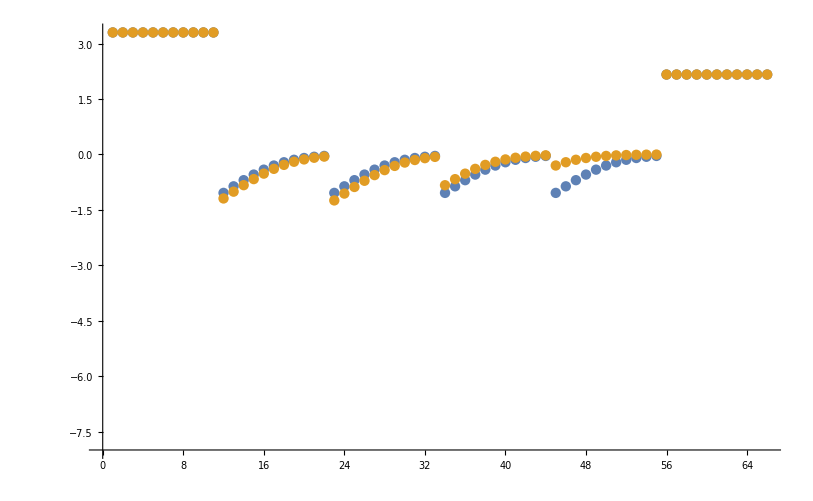

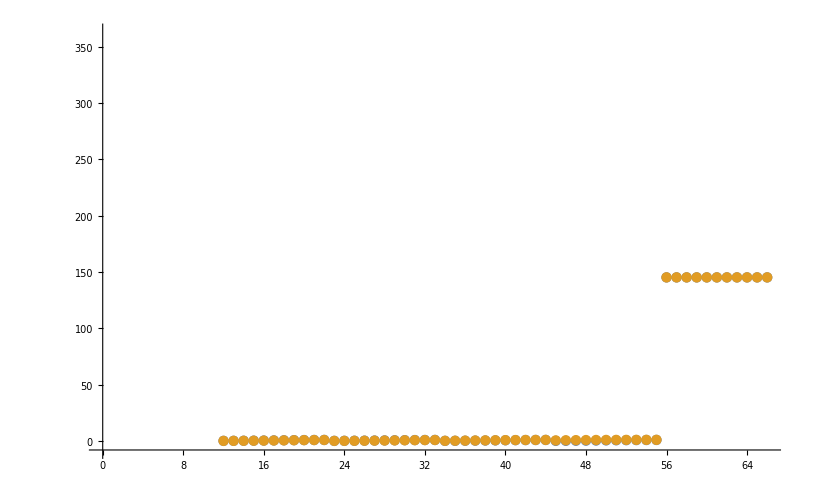

```mathematica
dataSetI=6;
ListPlot[Log10[{fittingData[[All,-1]],filteredDataList[[dataSetI,3]]}], AxesOrigin->{0,-8}]
ListPlot[{fittingData[[All,-1]],filteredDataList[[dataSetI,3]]}, AxesOrigin->{0,-8}]
```

### Parameter Distribution

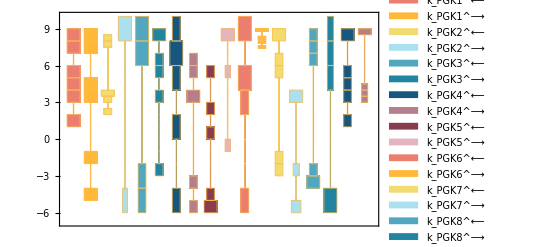

```mathematica
DistributionChart[Transpose[Log10[filteredDataList[[1;;6,2]]]],ChartElementFunction->"HistogramDensity","PlotRange"->{-7,10},ChartLegends-> rateConstsSub[[All,2]]/.Reverse/@rateConstsSub,ChartStyle-> 24]
```

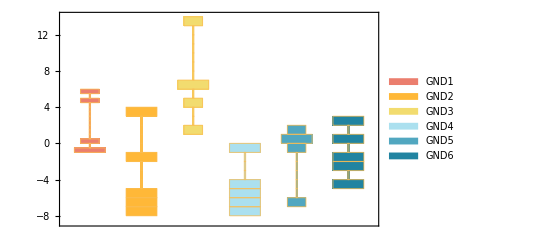

```mathematica
{ratios, plotLegend} = getElementaryKeqs[filteredDataList, rateConstsSub];
DistributionChart[Log10[Transpose@ratios],ChartElementFunction->"HistogramDensity",ChartLegends-> plotLegend,ChartStyle-> 24](*Histogram*)
```

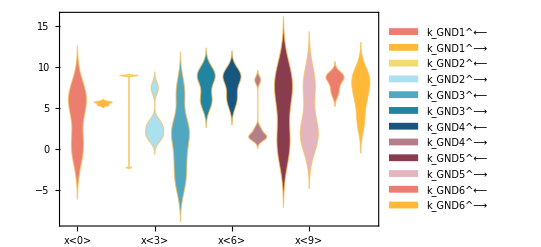

```mathematica
DistributionChart[Transpose[Log10[filteredDataList[[All,2]]]],ChartLabels-> rateConstsSub[[All,2]],"PlotRange"->{-7,10},ChartLegends-> rateConstsSub[[All,2]]/.Reverse/@rateConstsSub,ChartStyle-> 24](*Smooth*)(*If the distribution is narrow, the smooth Kernel outputs an error*)
```

### Data Error Distribution

```mathematica
errors=
Table[
	fittingData[[i,-1]]-filteredDataList[[j,3,i]],
 {j,1,Length@filteredDataList},{i,1,Length@filteredDataList[[1,3]]}];
```

```mathematica
funcNames=
Table[
	StringCases[func,RegularExpression[FileNameJoin[{inputPath , "(.*)\\.txt"}, OperatingSystem->$OperatingSystem]]->"$1"][[1]],{func,fittingData[[All,-2]]}]; (* fix later*);
```

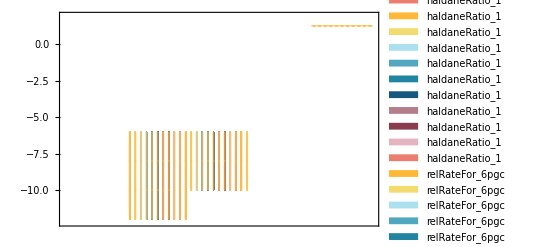

```mathematica
DistributionChart[Transpose[Log10[errors]],ChartElementFunction->"HistogramDensity",ChartLegends-> funcNames,ChartStyle-> 24](*Histogram*)
```

#### Cluster Parameters

```mathematica
(*clusters=FindClusters[Log10[filteredDataListRed[[All,2]]],Method->{"Agglomerate","Linkage"->"Complete","SignificanceTest"->{"Gap","Tolerance"->0.0001}}];(**)*)
clusters=FindClusters[Log10[filteredDataList[[1;;6,2]]],Method->{"Optimize","Iterations"->2}];
medianParamCluster=Table[Median[clusters[[cluster,All,param]]],{cluster,Length[clusters]},{param,Length[clusters[[1,1]]]}](*Switch to log space and use mean?*);
clusterSqdRes=Table[(clusters[[cluster,paramSet,param]]-medianParamCluster[[cluster,param]])^2,{cluster,Length[clusters]},{paramSet,Length[clusters[[cluster]]]},{param,Length[clusters[[1,1]]]}];
clusterSSE=Table[Total[clusterSqdRes[[cluster,paramSet]]],{cluster,Length[clusterSqdRes]},{paramSet,Length[clusterSqdRes[[cluster]]]}];
bestClusterSSE=Table[SortBy[clusterSSE[[cluster]],Less],{cluster,Length[clusterSSE]}][[All,1]];
finalClusterParams={};
Table[If[clusterSSE[[cluster,paramSet]]==bestClusterSSE[[cluster]],finalClusterParams=Append[finalClusterParams,clusters[[cluster,paramSet]]]],{cluster,Length[clusterSSE]},{paramSet,Length[clusterSSE[[cluster]]]}];
```

#### Print Representative Parameter Sets for Each Cluster (Optional)

```mathematica
TableForm[finalClusterParams]
```

8.99748 | 8.33165 | 3.65551 | 8.41034 | 9. | 6.17915 | 8.24867 | 5.54191 | -4.23708 | 5.0768 | 5.06688 | 8.96013 | 6.29732 | 3.81841 | -2.1041 | -4.69709 | 4.0749 | 4.00532

#### Parameter Cluster Plots (Optional)

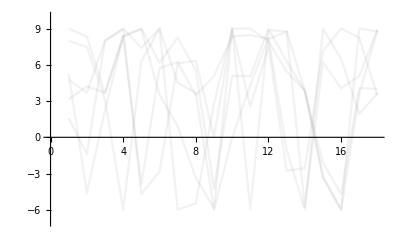

{-Graphics-}

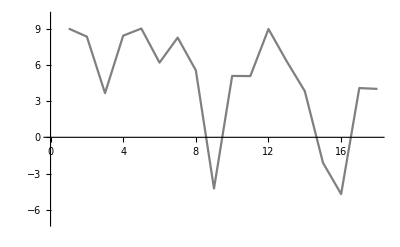

```mathematica
ListPlot[Log10[filteredDataList[[1;;6,2]]],"Joined"-> True,"PlotRange"->{-7,10},PlotStyle->Opacity[.1,Gray]](*All parameter sets*)
ListPlot[#,"Joined"-> True,"PlotRange"->{-7,10},PlotStyle->Opacity[.1,Gray]]&/@clusters
(*All parameter set clusters*)
ListPlot[#,"Joined"-> True,"PlotRange"->{-7,10},PlotStyle->Opacity[1,Gray]]&/@finalClusterParams(*Representative parameter sets*)
```

### Recalculate Enzyme Parameters for all Candidate Rate Constant Sets

```mathematica
enzymeSub= parameter[rxnName<>"_total"]-> 1;
assumedSaturatingConc=1;
paramSet = 1;
dataHeader = Import[dataFilePath][[1]];
paramFitSub=Thread[rateConstsSub[[All,1]]->filteredDataList[[paramSet,2]]];
```

```mathematica
backCalculateKms[rxn, kmList, relativeRateForward, relativeRateReverse,metSatForSub, metSatRevSub, paramFitSub, assumedSaturatingConc, rxnName]//TableForm
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of Solve::ratnz will be suppressed during this calculation.

data value | predicted value | error in %
0.000085 | 0.0000849964 | 0.00423497
0.000011 | 0.000011 | 0.000382447
0.0035 | 0.00349397 | 0.172288
0.0025 | 0.00249693 | 0.122993

```mathematica
backCalculateKcats[rxn, kcatList, absoluteRateForward, absoluteRateReverse, paramFitSub, enzymeSub, assumedSaturatingConc]//TableForm
```

data value | predicted value | error in %
2327.18 | 2327.18 | 0.0000555702

```mathematica
backCalculateRatios[haldaneRatiosList[[1]], KeqList[[1,3]], paramFitSub]//TableForm
```

data value | predicted value | error in %
1900 | 1900. | 3.69725×10^-6

```mathematica
backCalculateRatios[haldaneRatiosList[[1]], KeqList[[1]][[3]], paramFitSub]//TableForm
```

data value | predicted value | error in %
1900 | 1900. | 3.69725×10^-6

```mathematica
backCalculateKic[fittingData, filteredDataList[[1]], dataHeader, inhibitionList]//TableForm
```

data value | predicted value | error in %

```mathematica
backCalculateKiu[fittingData, filteredDataList[[1]], dataHeader, inhibitionList]//TableForm
```

data value | predicted value | error in %

#### Export rate back calculated parameter error distribution

```mathematica
dataHeader = Import[dataFilePath][[1]];

{predictedParameters, predictedParameterErrors} = exportPredictedParametersAndErrors[rxn, rxnName, fitLabel, flagFitType, numFits,KeqList, kmList,s05List, kcatList, inhibitionList, otherParmsList, absoluteRateForward, absoluteRateReverse, relativeRateForward, relativeRateReverse, haldaneRatiosList,  metSatForSub, metSatRevSub, rateConstsSub, assumedSaturatingConc, fittingData, filteredDataList, dataHeader];

BoxWhiskerChart[Transpose@predictedParameterErrors[[3;;]], ChartLabels->{predictedParameterErrors[[1]]}]
```

Set::shape: Lists {predictedParameters,predictedParameterErrors} and exportPredictedParametersAndErrors[((6pgc)^c+nadp^c⇌co2^c+nadph^c+ru5p__D^c)^GND,GND,«20»,{Priority,6pgc[c],co2[c],nadp[c],nadph[c],ru5p__D[c],param_GND_total,param_pH,param_Temp,FileFlag,Target_Data}] are not the same shape.

Part::take: Cannot take positions 3 through -1 in predictedParameterErrors.

Part::partd: Part specification predictedParameterErrors⟦1⟧ is longer than depth of object.

BoxWhiskerChart::ldata: Transpose[predictedParameterErrors⟦3;;All⟧] is not a valid dataset or list of datasets.

BoxWhiskerChart[Transpose[predictedParameterErrors⟦3;;All⟧],ChartLabels→{predictedParameterErrors⟦1⟧}]

## Export data

```mathematica
directoryExport = "C:\\Users\\Daniel Zielinski\\Desktop\\MASSpy Work\\"
CreateDirectory[directoryExport<>ToLowerCase[rxnName]]
indexLastGoodFit = 10;
```

C:\Users\Daniel Zielinski\Desktop\MASSpy Work\

C:\Users\Daniel Zielinski\Desktop\MASSpy Work\pfk2

```mathematica
rateConstsString = ToString/@rateConstsSub[[All,1]];
Export[directoryExport <>ToLowerCase[rxnName]<>"\\rateconst_labels_"<>ToLowerCase[rxnName]<>".txt",rateConstsString]
```

C:\Users\Daniel Zielinski\Desktop\MASSpy Work\pfk2\rateconst_labels_pfk2.txt

```mathematica
Export[directoryExport <>ToLowerCase[rxnName]<>"\\S_"<>ToLowerCase[rxnName]<>".txt",S[enzymeModel]]
```

C:\Users\Daniel Zielinski\Desktop\MASSpy Work\pfk2\S_pfk2.txt

```mathematica
ToString/@getSpecies[enzymeModel]
Export[directoryExport <>ToLowerCase[rxnName]<>"\\species_"<>ToLowerCase[rxnName]<>".txt",ToString/@getSpecies[enzymeModel]]
```

{E_PFK2[c],E_PFK2[c]&f6p,E_PFK2[c]&fdp,E_PFK2[c]&f6p&atp,adp[c],atp[c],f6p[c],fdp[c],E_PFK2[c]&fdp&adp}

C:\Users\Daniel Zielinski\Desktop\MASSpy Work\pfk2\species_pfk2.txt

```mathematica
ToString/@getReactions[enzymeModel]
Export[directoryExport <>ToLowerCase[rxnName]<>"\\reactions_"<>ToLowerCase[rxnName]<>".txt",ToString/@getReactions[enzymeModel]]
```

{PFK21: E_PFK2[c] + f6p[c] <=> E_PFK2[c]&f6p,PFK22: E_PFK2[c]&fdp <=> E_PFK2[c] + fdp[c],PFK23: atp[c] + E_PFK2[c]&f6p <=> E_PFK2[c]&f6p&atp,PFK24: E_PFK2[c]&fdp&adp <=> adp[c] + E_PFK2[c]&fdp,PFK25: E_PFK2[c]&f6p&atp <=> E_PFK2[c]&fdp&adp}

C:\Users\Daniel Zielinski\Desktop\MASSpy Work\pfk2\reactions_pfk2.txt

```mathematica
solEnz = Import["C:/MASSef/examples/"<>mainFolder <>"/input/enzSol_"<>rxnName<>"_.m"];
```

```mathematica
speciesStrings = ToString/@solEnz[[All,1]]
Export[directoryExport <>ToLowerCase[rxnName]<>"\\equation_labels_"<>ToLowerCase[rxnName]<>".txt",ToString/@solEnz[[All,1]]];
```

{E_PFK2[c],E_PFK2[c]&f6p,E_PFK2[c]&fdp,E_PFK2[c]&f6p&atp,E_PFK2[c]&fdp&adp}

```mathematica
pythonSubList = Thread[Variables[solEnz[[1,2]]]->(ToString/@Variables[solEnz[[1,2]]])];
ToPython[solEnz[[1,2]]/.pythonSubList]
Do[
Export[directoryExport <>ToLowerCase[rxnName]<>"\\equation_"<>speciesStrings[[i]]<>"_"<>ToLowerCase[rxnName]<>".txt",ToPython[solEnz[[i,2]]/.pythonSubList]];,{i,1,Length[solEnz]}]
```

-((-(k_PFK21_rev*k_PFK22_fwd*k_PFK23_rev*k_PFK24_fwd*param_PFK2_total) - k_PFK21_rev*k_PFK22_fwd*k_PFK24_fwd*k_PFK25_fwd*param_PFK2_total - atp(c)*k_PFK22_fwd*k_PFK23_fwd*k_PFK24_fwd*k_PFK25_fwd*param_PFK2_total - k_PFK21_rev*k_PFK22_fwd*k_PFK23_rev*k_PFK25_rev*param_PFK2_total - adp(c)*k_PFK21_rev*k_PFK23_rev*k_PFK24_rev*k_PFK25_rev*param_PFK2_total)/(atp(c)*f6p(c)*k_PFK21_fwd*k_PFK22_fwd*k_PFK23_fwd*k_PFK24_fwd + f6p(c)*k_PFK21_fwd*k_PFK22_fwd*k_PFK23_rev*k_PFK24_fwd + k_PFK21_rev*k_PFK22_fwd*k_PFK23_rev*k_PFK24_fwd + fdp(c)*k_PFK21_rev*k_PFK22_rev*k_PFK23_rev*k_PFK24_fwd + adp(c)*fdp(c)*k_PFK21_rev*k_PFK22_rev*k_PFK23_rev*k_PFK24_rev + atp(c)*f6p(c)*k_PFK21_fwd*k_PFK22_fwd*k_PFK23_fwd*k_PFK25_fwd + f6p(c)*k_PFK21_fwd*k_PFK22_fwd*k_PFK24_fwd*k_PFK25_fwd + k_PFK21_rev*k_PFK22_fwd*k_PFK24_fwd*k_PFK25_fwd + fdp(c)*k_PFK21_rev*k_PFK22_rev*k_PFK24_fwd*k_PFK25_fwd + atp(c)*f6p(c)*k_PFK21_fwd*k_PFK23_fwd*k_PFK24_fwd*k_PFK25_fwd + atp(c)*k_PFK22_fwd*k_PFK23_fwd*k_PFK24_fwd*k_PFK25_fwd + atp(c)*fdp(c)*k_PFK22_rev*k_PFK23_fwd*k_PFK24_fwd*k_PFK25_fwd + adp(c)*fdp(c)*k_PFK21_rev*k_PFK22_rev*k_PFK24_rev*k_PFK25_fwd + adp(c)*atp(c)*f6p(c)*k_PFK21_fwd*k_PFK23_fwd*k_PFK24_rev*k_PFK25_fwd + adp(c)*atp(c)*fdp(c)*k_PFK22_rev*k_PFK23_fwd*k_PFK24_rev*k_PFK25_fwd + atp(c)*f6p(c)*k_PFK21_fwd*k_PFK22_fwd*k_PFK23_fwd*k_PFK25_rev + f6p(c)*k_PFK21_fwd*k_PFK22_fwd*k_PFK23_rev*k_PFK25_rev + k_PFK21_rev*k_PFK22_fwd*k_PFK23_rev*k_PFK25_rev + fdp(c)*k_PFK21_rev*k_PFK22_rev*k_PFK23_rev*k_PFK25_rev + adp(c)*fdp(c)*k_PFK21_rev*k_PFK22_rev*k_PFK24_rev*k_PFK25_rev + adp(c)*atp(c)*f6p(c)*k_PFK21_fwd*k_PFK23_fwd*k_PFK24_rev*k_PFK25_rev + adp(c)*atp(c)*fdp(c)*k_PFK22_rev*k_PFK23_fwd*k_PFK24_rev*k_PFK25_rev + adp(c)*f6p(c)*k_PFK21_fwd*k_PFK23_rev*k_PFK24_rev*k_PFK25_rev + adp(c)*k_PFK21_rev*k_PFK23_rev*k_PFK24_rev*k_PFK25_rev + adp(c)*fdp(c)*k_PFK22_rev*k_PFK23_rev*k_PFK24_rev*k_PFK25_rev))

```mathematica
(*NEED TO GRAB THE RATE CONST DATA FROM CLUSTERS*)
```

```mathematica
Export[directoryExport <>ToLowerCase[rxnName]<>"\\rateconst_clusters_"<>ToLowerCase[rxnName]<>".txt",filteredDataList[[1;;indexLastGoodFit,2]]]
```

C:\Users\Daniel Zielinski\Desktop\MASSpy Work\pfk2\rateconst_clusters_pfk2.txt

```mathematica
solRateEq = Import["C:/MASSef/examples/"<>mainFolder <>"/input/absoluteFlux_"<>rxnName<>"_.m"];
```

```mathematica
pythonSubList = Thread[Variables[solRateEq[[2]]]->(ToString/@Variables[solRateEq[[2]]])];
```

```mathematica
Export[directoryExport <>ToLowerCase[rxnName]<>"\\rateLaw_"<>ToLowerCase[rxnName]<>".txt",ToPython[solRateEq[[2]]/.pythonSubList]]
```

C:\Users\Daniel Zielinski\Desktop\MASSpy Work\pfk2\rateLaw_pfk2.txt